# Dust echo model

```mathematica
SetDirectory["/Users/cecilia/Dropbox (ASU)/Tywin_IC200530/numerics"]
```

/Users/cecilia/Dropbox (ASU)/Tywin_IC200530/numerics

### Constants

use eV everywhere for sanity' s sake

```mathematica
c=299792458  ; (* m/s *)
```

```mathematica
hbar = 6.582 10^−22  10^6  (* eV s *)
```

6.582×10^-16

```mathematica
HztoeV=2 Pi hbar  (* note: I use E = h nu , with  h and NOT hbar *)
```

4.13559×10^-15

```mathematica
ergtoev=6.242 10^11 ;
```

```mathematica
lunit=10^46 ergtoev
```

6.242×10^57

```mathematica
dist=1397.25 *  3.086 10^24 (* distance to Tywin in cm *)
```

4.31191×10^27

```mathematica
kb=8.617 ×10^−5  ;(* eV K−1 ; Boltzmann constant *)
```

## Data: Take SED from our draft, fig 6

table of data. The first three points are the IR tail and the rest is from ZTF (?). The function plotted is nu F(nu). Units are Hz (x - axis) and ergs s^-1 cm^-2  (y - axis).

```mathematica
tabdata={
{10^14.149046793760833,10^-11.469635627530364},
{10^14.280762564991335,10^-11.870445344129553},
{10^14.395147313691508,10^-12.445344129554655},
{10^14.580589254766032,10^-12.356275303643724},
{10^14.675909878682843,10^-12.445344129554655},
{10^14.802426343154247,10^-12.408906882591092},
{10^15.126516464471404,10^-12.441295546558704}} ;
```

Change units : new units are  eV (x - axis) and ergs s^-1 cm^-2 (y - axis).

```mathematica
tabdataconv=Table[{tabdata[[i,1]]*HztoeV,tabdata[[i,2]]},{i,1,Length[tabdata]}]
```

{{0.582887,3.39129×10^-12},{0.789406,1.34758×10^-12},{1.02727,3.58638×10^-13},{1.57444,4.40276×10^-13},{1.96086,3.58638×10^-13},{2.624,3.90026×10^-13},{5.53419,3.61997×10^-13}}

IR data points only :

```mathematica
tabdataIR=Take[tabdataconv,3]
```

{{0.582887,3.39129×10^-12},{0.789406,1.34758×10^-12},{1.02727,3.58638×10^-13}}

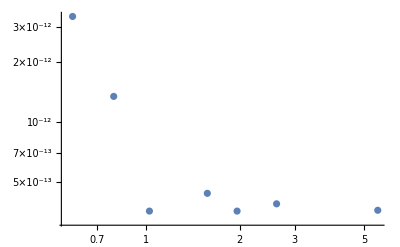

```mathematica
plot1=ListLogLogPlot[tabdataconv]
```

## set up Blackbody function :

see below, it' s a generalized BB, where alpha = 2 is the normal BB.  The function dnde is the number of photons per unit energy, per unit area per unit time

```mathematica
dnde[e_,t_,l_,alpha_]:=(Gamma[alpha + 2] PolyLog[alpha+2,1])^-1 (l*lunit )/(4 Pi dist^2 t^2) (e/t)^alpha (Exp[e/t]+1)^-1
```

same function, converted so that the units are ergs s^1 cm^-1  :

```mathematica
sed[e_,t_,l_,alpha_]:=e^2 dnde[e,t,l,alpha]/ergtoev
```

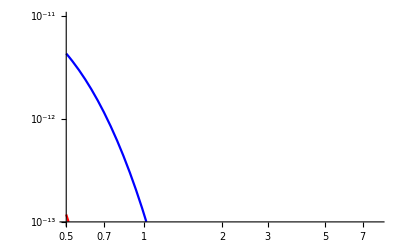

```mathematica
LogLogPlot[{sed[e,0.03,1,0],sed[e,0.05,1,0],sed[e,0.1,1,0]},{e,0.5, 8},PlotStyle->{Green,Red,Blue},PlotRange->{10^-13, 10^-11}]
```

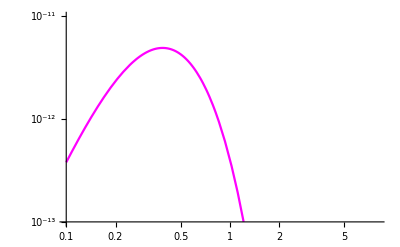

```mathematica
plot2=LogLogPlot[{sed[e,0.1,0.17,1.8]},{e,0.1, 8},PlotStyle->{Magenta},PlotRange->{10^-13, 10^-11}]
```

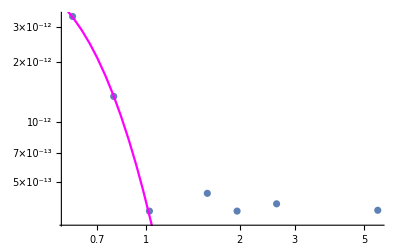

```mathematica
Show[{plot1,plot2}]
```

convert temperature from eV to K :

```mathematica
tbest=0.1 /kb
```

1160.5

perfect value, in the right ballpark!

try to fit remaining part of the spectrum :

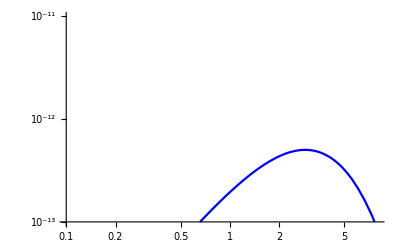

```mathematica
plot3=LogLogPlot[{sed[e,1.3,0.04,0]},{e,0.1, 8},PlotStyle->{Blue},PlotRange->{10^-13, 10^-11}]
```

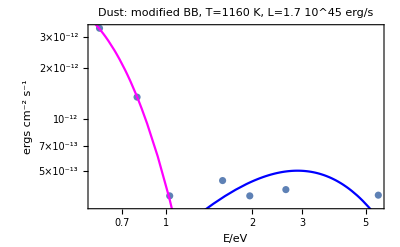

```mathematica
Show[{plot1,plot2,plot3},Frame-> True,FrameLabel->{ Style["E/eV",18],Style["ergs"Subscripted[cm["",-2] ,1,-1]Subscripted[s["",-1] ,1,-1]]},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Helvetica"],PlotLabel-> Style["Dust: modified BB, T=1160 K, L=1.7 10^45 erg/s",14],ImageSize -> { 500}]
```